## Homework 3

## 4. Joukowski Transform

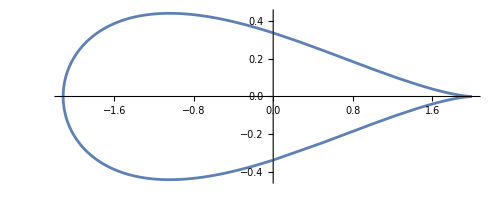

```mathematica
(*Define the Joukowski transform*)
joukowskiTransform[z_]:=z+1/z

(*Parametrize the circle in the z-plane*)
r=6/5;
center=-1/5;
z[θ_]:=r*Exp[I*θ]+center

(*Apply the Joukowski transform to the circle parametrization*)
w[θ_]:=joukowskiTransform[z[θ]]

(*Plot the image of the circle under the Joukowski transform*)
p1=ParametricPlot[{Re[w[θ]],Im[w[θ]]},{θ,0,2*Pi},AspectRatio->Automatic]
```

We know that the potential flow around a cylinder (circle in the v - plane) with circulation Γ and far-field velocity U is given by the complex potential Φ(v)=U(v+1/v)+(i Γ)/(2 π)Log(v). For the simplest case, we choose Φ(v)=v+1/v+i Log(v).

So for w plane, we can:
- First, solve for z given w by inverting w=z+1/z​ to get z(w) =1/2 (w+√(-4+w^2)) for one branch.
- Then, solve for v given z, thus mapping z to v and for v, we have the solution Φ(v).
Therefore, the solution in the w plane is f(w)=Φ(v(z(w))).

```mathematica
Reduce[z+1/z==w,{z}]
```

z==1/2 (w-√(-4+w^2))||z==1/2 (w+√(-4+w^2))

Stream Plot

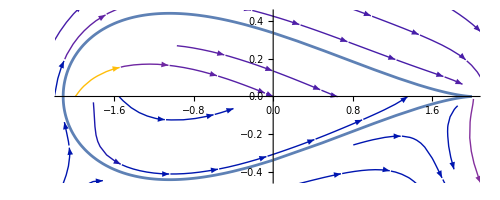

```mathematica
(*Define the potential function Φ(z)*)
U=1; (*Far away velocity*)
Γ=1; (*Circulation-You can adjust this as needed*)

Phi[v_]:= v+1/v+I Log[v]
v[z_]:=5/6 z+1/6
(*z[w_]:=1/2 (w+√(-4+w^2))*)
z[w_]:=1/2 (w+Exp[1/2(Log[w+2]+Log[w-2])])

(*Calculate the velocity field V(z)*)
vel[w_]:=D[Phi[v[z[ww]]],ww]/.{ww->w}

(*To use StreamPlot,we need the real and imaginary parts of the velocity field*)
velocityField[w_]:=Through[{Re,Minus@* Im}[vel[w]]]

(*Plot the streamlines in the w-plane*)
p2=StreamPlot[velocityField[x+I y],{x,-3,3},{y,-3,3},AspectRatio->Automatic];

Show[p1,p2]
```